# CFD Schemes For Testing

```mathematica
Clear["`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks

```mathematica
$ProcessorCount
```

14

## Kim Pentadiagonal 6th Order

```mathematica
kimPent6th[n_]:=Module[{P,Q,α,β,a0,a1,a2,a3,γ01,γ02,γ10,γ12,γ13,γ20,γ21,γ23,γ24,γS12,γS13,γS20,γS21,γS23,γS24,b22Filter,b00,b01,b02,b03,b04,b05,b06,b10,b11,b12,b13,b14,b15,b16,b20,b21,b22,b23,b24,b25,b26,bS11,bS12,bS13,bS14,bS15,bS16,bS21,bS22,bS23,bS24,bS25,bS26},
α=0.5862704032801503;
β=0.09549533555017055;
a1=0.6431406736919156;
a2=0.2586011023495066;
a3=0.007140953479797375;

γ01=5.912678614078549;
γ02=3.775623951744012;
γ10=0.08360703307833438;
γ12=2.058102869495757;
γ13=0.9704052014790193;
γ20=0.03250008295108466;
γ21=0.3998040493524358;
γ23=0.7719261277615860;
γ24=0.1626635931256900;

b01=-3.456878182643609;
b02=5.839043358834730;
b03=1.015886726041007;
b04=-0.2246526470654333;
b05=0.08564940889936562;
b06=-0.01836710059356763;
b00=-(b01+b02+b03+b04+b05+b06);
Print[b00];

b10=-0.3177447290722621;
b12=-0.02807631929593225;
b13=1.593461635747659;
b14=0.2533027046976367;
b15=-0.03619652460174756;
b16=0.004080281419108407;
b11=-(b10+b12+b13+b14+b15+b16);

b20=-0.1219006056449124;
b21=-0.6301651351188667;
b23=0.6521195063966084;
b24=0.3938843551210350;
b25=0.01904944407973912;
b26=-0.001027260523947668;
b22=-(b20+b21+b23+b24+b25+b26);

γS12=(γ12-γ10 γ02)/(1-γ10 γ01);
γS13=γ13/(1-γ10 γ01);
γS21=(γ10 γ21-γ20)/(γ10-γ20 γ12);
γS23=(γ10 γ23-γ20 γ13)/(γ10-γ20 γ12);
γS24=(γ10 γ24)/(γ10-γ20 γ12);

bS11=(b11-γ10 b01)/(1-γ10 γ01);
bS12=(b12-γ10 b02)/(1-γ10 γ01);
bS13=(b13-γ10 b03)/(1-γ10 γ01);
bS14=(b14-γ10 b04)/(1-γ10 γ01);
bS15=(b15-γ10 b05)/(1-γ10 γ01);
bS16=(b16-γ10 b06)/(1-γ10 γ01);

bS21=(γ10 b21-γ20 b11)/(γ10-γ20 γ12);
bS22=(γ10 b22-γ20 b12)/(γ10-γ20 γ12);
bS23=(γ10 b23-γ20 b13)/(γ10-γ20 γ12);
bS24=(γ10 b24-γ20 b14)/(γ10-γ20 γ12);
bS25=(γ10 b25-γ20 b15)/(γ10-γ20 γ12);
bS26=(γ10 b26-γ20 b16)/(γ10-γ20 γ12);

P=Table[0,{i,n},{j,n}];
P[[1,1]]=1;
P[[1,2]]=γS12;
P[[1,3]]=γS13;

P[[2,1]]=γS21;
P[[2,2]]=1;
P[[2,3]]=γS23;
P[[2,4]]=γS24;

P[[n,n]]=1;
P[[n,n-1]]=γ01;
P[[n,n-2]]=γ02;

P[[n-1,n]]=γ10;
P[[n-1,n-1]]=1;
P[[n-1,n-2]]=γ12;
P[[n-1,n-3]]=γ13;

P[[n-2,n]]=γ20;
P[[n-2,n-1]]=γ21;
P[[n-2,n-2]]=1;
P[[n-2,n-3]]=γ23;
P[[n-2,n-4]]=γ24;

Do[
P[[i,i]]=1;
If[(j==i-2)||(j==i+2), 
P[[i,j]]=β,
If[(j==i-1)||(j==i+1),
P[[i,j]]=α
]
]
,{i,3,n-3},{j,1,n}];

Q=Table[0,{i,n},{j,n}];
Q[[1,1]]=bS11;
Q[[1,2]]=bS12;
Q[[1,3]]=bS13;
Q[[1,4]]=bS14;
Q[[1,5]]=bS15;
Q[[1,6]]=bS16;

Q[[2,1]]=bS21;
Q[[2,2]]=bS22;
Q[[2,3]]=bS23;
Q[[2,4]]=bS24;
Q[[2,5]]=bS25;
Q[[2,6]]=bS26;

Q[[n,n]]=-b00;
Q[[n,n-1]]=-b01;
Q[[n,n-2]]=-b02;
Q[[n,n-3]]=-b03;
Q[[n,n-4]]=-b04;
Q[[n,n-5]]=-b05;
Q[[n,n-6]]=-b06;

Q[[n-1,n]]=-b10;
Q[[n-1,n-1]]=-b11;
Q[[n-1,n-2]]=-b12;
Q[[n-1,n-3]]=-b13;
Q[[n-1,n-4]]=-b14;
Q[[n-1,n-5]]=-b15;
Q[[n-1,n-6]]=-b16;

Q[[n-2,n]]=-b20;
Q[[n-2,n-1]]=-b21;
Q[[n-2,n-2]]=-b22;
Q[[n-2,n-3]]=-b23;
Q[[n-2,n-4]]=-b24;
Q[[n-2,n-5]]=-b25;
Q[[n-2,n-6]]=-b26;

Do[
If[(j==i-3), 
Q[[i,j]]=-a3,
If[(j==i+3),
Q[[i,j]]=a3,
If[(j==i-2), 
Q[[i,j]]=-a2,
If[(j==i+2),
Q[[i,j]]=a2,
If[(j==i-1), 
Q[[i,j]]=-a1,
If[(j==i+1),
Q[[i,j]]=a1
]
]
]
]
]
]
,{i,3,n-3},{j,1,n}];
Return[{Q,P}]
]
kimPent6th[20][[1]]//MatrixForm
kimPent6th[20][[2]]//MatrixForm
```

-3.24068

(-2.33321 | -1.02097 | 2.98329 | 0.538081 | -0.0857445 | 0.0111061 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.296033 | -1.50549 | 0.16354 | 1.47735 | 0.165628 | -0.0130691 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00102726 | -0.0190494 | -0.393884 | -0.65212 | 0.31196 | 0.630165 | 0.121901
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00408028 | 0.0361965 | -0.253303 | -1.59346 | 0.0280763 | 1.46883 | 0.317745
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0183671 | -0.0856494 | 0.224653 | -1.01589 | -5.83904 | 3.45688 | 3.24068)

-3.24068

(1 | 3.44587 | 1.91909 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0554085 | 1 | 1.97387 | 0.813458 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.162664 | 0.771926 | 1 | 0.399804 | 0.0325001
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.970405 | 2.0581 | 1 | 0.083607
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.77562 | 5.91268 | 1)

```mathematica
kimPent6thFilters[n_,κc_,ϵ_,Matrix_]:=Module[{R,S, α, β,γ, bS,γS,b,a,A,c,d},
A=30-5Cos[κ]+10Cos[2κ]-3Cos[3κ];
α=-(30Cos[κ]+2Cos[3κ])/A;
β=(18+9Cos[κ]+6Cos[2κ]-Cos[3κ])/(2A);

a={0,30/A Cos[κ/2]^4,0,0};
a[[3]]=-(2a[[2]])/5;
a[[4]]=a[[2]]/15;
a[[1]]=-2(a[[2]]+a[[3]]+a[[4]]);

c=1+β(5+4β+60 β^2)+5(1+3β+10 β^2)α+2(4+11β)α^2+5 α^3;
d=(1-β)(1+6β+60 β^2)+(5+35β-29 β^2)α+(9-5β)α^2;

γ={{1,1/c(α(1+α)(1+4α)+2α(7+3α)β+24(1-α)β^2-80 β^3),1/c(α^3+(1+3α+14 α^2)β+46α β^2+60 β^3)},{1/d(10 β^2(8β-1)+(1+4β+81 β^2)α+5(1+8β)α^2+9 α^3),1,1/d(α(1+5α+9 α^2)+α(5+36α)β+(55α-1)β^2+10 β^3),β/d(1+5α+9 α^2+5(1+7α)β+50 β^2)},{β,α,1,α,β}};
γ[[1]]=γ[[1]]/.κ->(1-3ϵ)κc;
γ[[2]]=γ[[2]]/.κ->(1-2ϵ)κc;
γ[[3]]=γ[[3]]/.κ->(1-1ϵ)κc;
(*Print["γ_(00 - 02): "<>ToString[γ[[1]]]];
Print["γ_(10 - 13): "<>ToString[γ[[2]]]];
Print["γ_(20 - 24): "<>ToString[γ[[3]]]];*)

b={a[[3]]+5a[[4]],a[[2]]-10a[[4]],0,a[[2]]-5a[[4]],a[[3]]+a[[4]],a[[4]]}/.κ->(1-1ϵ)κc;
b[[3]]=-(Sum[b[[i]],{i,1,6}]);
(*Print["b_(20 - 25): "<>ToString[b]];*)

γS={{1,(γ[[2,3]]-γ[[2,1]]*γ[[1,3]])/(1-γ[[2,1]]*γ[[1,2]]),γ[[2,4]]/(1-γ[[2,1]]*γ[[1,2]])},{(γ[[2,1]]*γ[[3,2]]-γ[[3,1]])/(γ[[2,1]]-γ[[3,1]]*γ[[2,3]]),1,(γ[[2,1]]*γ[[3,4]]-γ[[3,1]]*γ[[2,4]])/(γ[[2,1]]-γ[[3,1]]*γ[[2,3]]),(γ[[2,1]]*γ[[3,5]])/(γ[[2,1]]-γ[[3,1]]*γ[[2,3]])}};
(*Print["(γ^*)_(11 - 13): "<>ToString[γ[[1]]]];
Print["(γ^*)_(21 - 24): "<>ToString[γ[[2]]]];*)

bS=Table[γ[[2,1]]*b[[i]],{i,2,6}]/(γ[[2,1]]-γ[[3,1]]*γ[[2,3]]);
(*Print["(b^*)_(21 - 25): "<>ToString[bS]];*)

β=β/.κ->κc;
α=α/.κ->κc;
a=a/.κ->κc;

(*Print["α: "<>ToString[α]];
Print["β: "<>ToString[β]];
Print["a_(0 - 3): "<>ToString[a]];*)

R=IdentityMatrix[n];
R[[1,2]]=γS[[1,2]];R[[1,3]]=γS[[1,3]];
R[[2,1]]=γS[[2,1]]; R[[2,3]]=γS[[2,3]]; R[[2,4]]=γS[[2,4]];
R[[n,n-1]]=γ[[1,2]];R[[n,n-2]]=γS[[1,3]];
R[[n-1,n]]=γ[[2,1]]; R[[n-1,n-2]]=γ[[2,3]]; R[[n-1,n-3]]=γ[[2,4]];
R[[n-2,n]]=γ[[3,1]]; R[[n-2,n-1]]=γ[[3,2]]; R[[n-2,n-3]]=γ[[3,4]]; R[[n-2,n-4]]=γ[[3,5]];
Do[
If[(j==i-2)||(j==i+2), 
R[[i,j]]=β,
If[(j==i-1)||(j==i+1),
R[[i,j]]=α
]
],{i,3,n-3},{j,1,n}];

S=Table[0,{i,n},{j,n}];
Do[S[[2,i]]=bS[[i]]; S[[n-2,n-i+1]]=b[[i]],{i,1,5}];
S[[n-2,n-5]]=b[[6]];
Do[
If[j>=i-3&&j<=i+3,
S[[i,j]]=a[[Abs[i-j]+1]]
]
,{i,3,n-3},{j,1,n}];

If[Matrix,
Return[{R,S}],
Return[{"α"->α, "β"->β, "a0"->a[[1]],"a1"->a[[2]],"a2"->a[[3]],"a3"->a[[4]],"γ01"->γ[[1,2]],"γ02"->γ[[1,3]], "γ10"->γ[[2,1]],"γ12"->γ[[2,3]],"γ13"->γ[[2,4]],"γ20"->γ[[3,1]],"γ21"->γ[[3,2]],"γ23"->γ[[3,4]],"γ24"->γ[[3,5]],"b20"->b[[1]],"b21"->b[[2]],"b22"->b[[3]],"b23"->b[[4]],"b24"->b[[5]],"b25"->b[[6]]}]
]
]
```

-3.24068

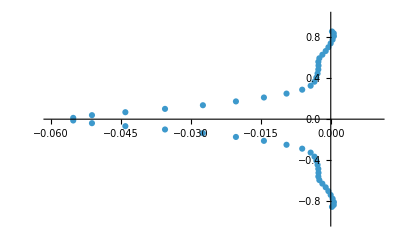

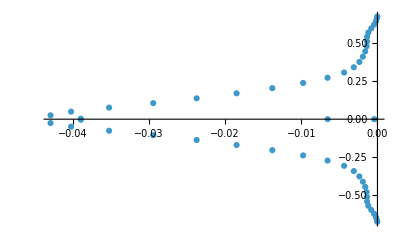

-Graphics-

```mathematica
{Q,P}=kimPent6th[50];
Q//MatrixForm;
P//MatrixForm;

{R,S}=kimPent6thFilters[50,0.85π,0,True];
R//MatrixForm;
S//MatrixForm;

noFilter=Eigenvalues[-Inverse[P].Q]/π;
filterAttempt=Eigenvalues[-Inverse[P].Q.(IdentityMatrix[50]+Inverse[R].S)]/π;

ComplexListPlot[noFilter,AspectRatio->1/GoldenRatio,PlotRange->{{-0.06,0.01},{-1,1}}]
ComplexListPlot[filterAttempt,AspectRatio->1/GoldenRatio,PlotRange->{All}]
ComplexListPlot[Eigenvalues[-Inverse[P].Q.(IdentityMatrix[50]+Inverse[R].S)]/π,AspectRatio->1/GoldenRatio,PlotRange->{All}]
```

## Testing New Matrices

### Building General Matrix

```mathematica
Clear[α,β,a1,a2,a3,yHat2,yHat1,yHat0,yHat]
Clear[γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j,-a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];

LHS[10]//MatrixForm
RHS[10]//MatrixForm
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

### Initialize Matrix and ŷ Definitions

```mathematica
PRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]

QRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
Pbuild[k_]:=Array[PRows[#1,#2,k]&,{k,k}];
Qbuild[k_]:=Array[QRows[#1,#2,k]&,{k,k}];

nateCoeffs={α->0.5573223518365282,β->0.076203478481807,a1->0.6694377318500324,a2->0.22598218207734894,a3->0.0040412447712016904,γ01->7.197716094824484,γ02->6.126551926460928,γ10->0.08918059126032331,γ12->1.5358275855335228,γ13->0.39888676733488315,γ20->0.014249184858449039,γ21->0.26879840403244193,γ23->1.0681671800782038,γ24->0.27905591015869174,a00->-3.445400951639534,a01->-5.687689758411866,a02->6.920468274013684,a03->2.8392090828531993,a04->-0.8151792182119252,a05->0.21744456676079005,a06->-0.028851995651904917,a10->-0.3406129751922464,a11->-1.3027478048845684,a12->0.6360810651517776,a13->0.9756407224469644,a14->0.030157398841492614,a15->0.001960705816633491,a16->-0.0004791121800322922,a20->-0.0595287580739372,a21->-0.5364452203671104,a22->-0.6798036396699008,a23->0.6082560121241458,a24->0.6344722261258422,a25->0.03463004120708508,a26->-0.001580661345977278};

LHSBarsNate={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.nateCoeffs),
γ13Bar->(γ13/(1-γ10*γ01)/.nateCoeffs),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.nateCoeffs),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.nateCoeffs),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.nateCoeffs)};

RHSBars1Nate=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.nateCoeffs;
RHSBars2Nate=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.nateCoeffs;

barCoeffsNate=Join[LHSBarsNate,RHSBars1Nate,RHSBars2Nate];

NateCoeffs=Join[nateCoeffs,barCoeffsNate];
```

### Optimization

```mathematica
κcList=Array[#&,50,{0.799,0.999}];
ϵList=Array[#&,50,{0,1/3}];

k=160;

{Q,P}={Qbuild[k],Pbuild[k]}/.NateCoeffs;

Clear[xx,yy]
```

```mathematica
LaunchKernels[8]
```

{Local (8),Local (8),Local (8),Local (8),Local (8),Local (8),Local (8),Local (8)}

```mathematica
ParallelEvaluate[Directory[]]
```

{C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks,C:\Users\jambl\OneDrive - Brigham Young University\Desktop\Research\Dr.Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks}

```mathematica
DistributeDefinitions[Q,P,κcList, ϵList,kimPent6thFilters,k]
```

{Q,P,κcList,ϵList,kimPent6thFilters,k}

```mathematica
maxrelist=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{xx,yy}];*)

{LHSNum, RHSNum}=kimPent6thFilters[k,κcList[[xx]]π,ϵList[[yy]], True];

mat=-Inverse[P].Q.(IdentityMatrix[k]+Inverse[LHSNum].RHSNum);
eigs=Eigenvalues[mat];
{{κcList[[xx]],ϵList[[yy]]},Max[Re[eigs]]},
{xx,1,Length@κcList},{yy,1,Length@ϵList}];
```

```mathematica
maxrelist//TableForm;
Dimensions@maxrelist

trimmed=Flatten[maxrelist,1];

stable={};
realVals={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]];
AppendTo[realVals,trimmed[[i,2]]]]
]

stable;
Length@stable

plotMax = {};
For[i=1,i<=Length@stable,i++,
AppendTo[plotMax,{stable[[i,1,1]],stable[[i,1,2]],stable[[i,2]]}];
]

ListPointPlot3D[plotMax,PlotRange->All,ImageSize->Large]
```

{50,50,2}

327

-Graphics3D-

```mathematica
stable[[187]]
stable[[386]]
stable[[916]]
stable[[921]]

kimPent6thFilters[20,0.9377755102040817π,22/147,False]
```

{{0.827571,3/49},-2.16463×10^-6}

{{0.856143,23/147},-4.8547×10^-6}

{{0.937776,22/147},-0.0000101963}

{{0.937776,12/49},-0.000152569}

{α→0.666563,β→0.166687,a0→-0.0000777636,a1→0.0000583227,a2→-0.0000233291,a3→3.88818×10^-6,γ01→0.0598943,γ02→0.396375,γ10→0.653284,γ12→0.580911,γ13→0.217728,γ20→0.169508,γ21→0.652458,γ23→0.652458,γ24→0.169508,b20→-0.000532813,b21→0.00266407,b22→-0.00532813,b23→0.00532813,b24→-0.00266407,b25→0.000532813}

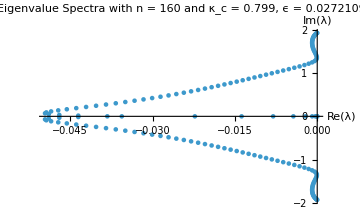
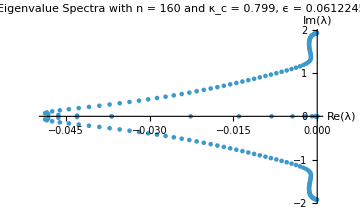
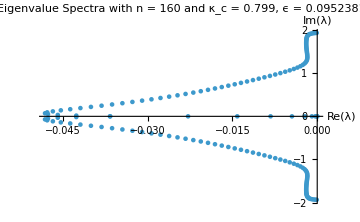
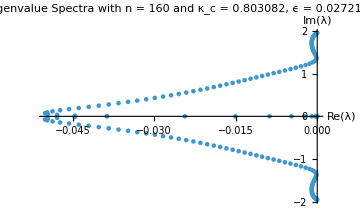
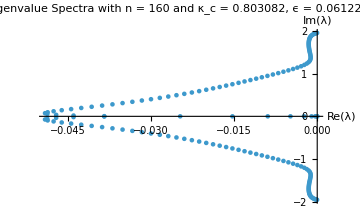
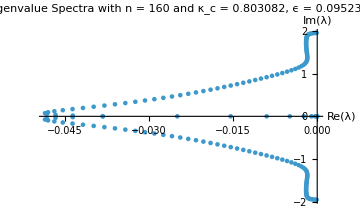
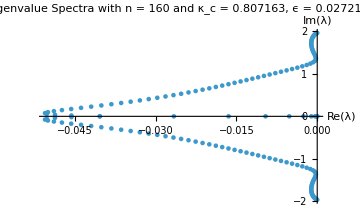
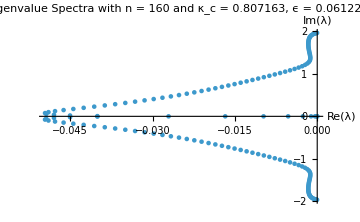

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
κc=stable[[m,1,1]];
ϵ=stable[[m,1,2]];


(*Eigenvalue Analysis*)
{LHSNum, RHSNum}=kimPent6thFilters[k,κc π,ϵ,True];

mat=-Inverse[P].Q.(IdentityMatrix[k]+Inverse[LHSNum].RHSNum);
eigs=Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","κ_c = ",ToString[κc],", ϵ = ",ToString[ϵ//N]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium],

{m,1,Length@stable,5}]
```